```mathematica
f[x_,y_]=(x+1)^(2/3)+(y-3)^(2/3)-4
g[x_,y_]=3 x^2-5 y^2-15
```

-4+(1+x)^(2/3)+(-3+y)^(2/3)

-15+3 x^2-5 y^2

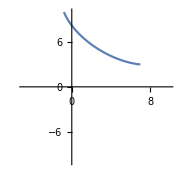

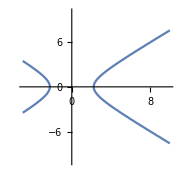

```mathematica
gr1=ContourPlot[f[x,y]==0,{x,-5,10},{y,-10,10},Axes->True,Frame->False,ImageSize->Small]
gr2=ContourPlot[g[x,y]==0,{x,-5,10},{y,-10,10},Axes->True,Frame->False,ImageSize->Small]
```

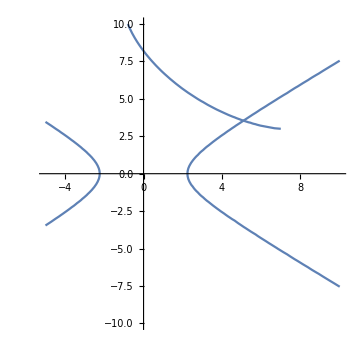

```mathematica
Show[gr1,gr2,ImageSize->Medium]
```

```mathematica
FindRoot[{f[x,y]==0,g[x,y]==0},{x,5},{y,5}]
```

{x→5.09045,y→3.54226}